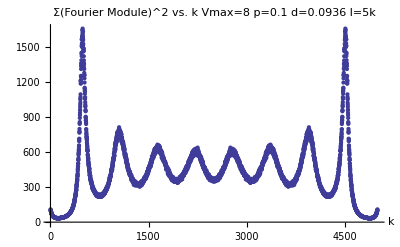

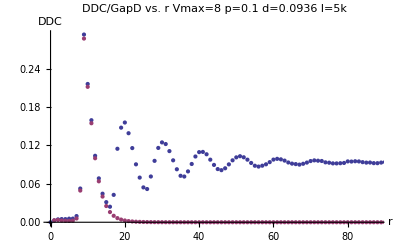

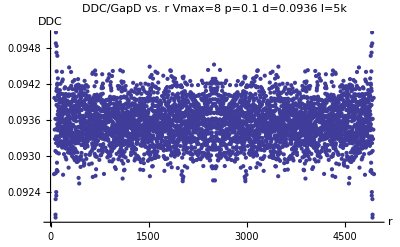

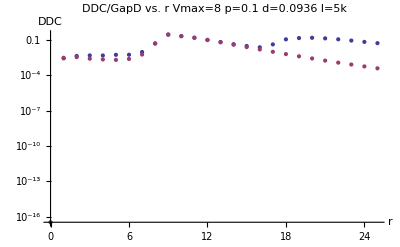

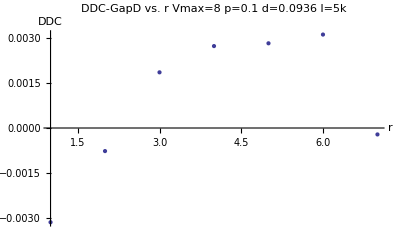

```mathematica
d="0.0936";
l="5";
v="8";
p="0.1";
fourier=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Fourier1D-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ddc=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/DDC-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
gf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapDFull-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
jj=StringToStream[v];
vmax= Read[jj,Number];
dif=Table[{i,ddc[[All,2]][[i]]-gf[[All,2]][[i]]},{i,1,vmax-1}];
ListPlot[fourier,PlotLabel->"Σ(Fourier Module)^2 vs. k Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k"," "},PlotRange->Full]
ListPlot[{ddc,gf},PlotLabel->"DDC/GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->{{0,88},Full},PlotLegend->{"DDC","Gap D."},LegendPosition->{1.1,-0.4},LegendSize->{0.4,0.6},LegendShadow->None]
ListPlot[{ddc,gf},PlotLabel->"DDC/GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->{Full}]
ListLogPlot[{ddc,gf},PlotLabel->"DDC/GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->{{0,25},Full}]
ListPlot[dif,PlotLabel->"DDC-GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"}]
```